```mathematica
spec200[p_]:=(19.2(1+(p/6)^2))/((1+p/3.7)^12(1+Exp[0.9-2p]));(*200 GeV*)
(*spec2[p_]:=(0.845(p+0.5)^2)/(1+p/6.8)^21;(*200 GeV*)  See Ref.charm_fik2 for details in pp collisions*)
spec55[p_]:=2497(1+p/1.95)^-5.5(p(1+(4/(0.1+p))^2))^-1;(*5.5 TeV*)
```

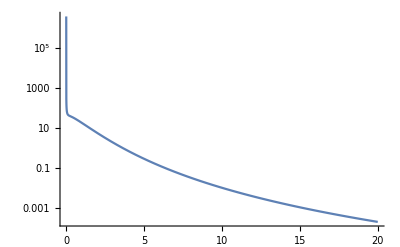

```mathematica
LogPlot[spec55[p],{p,0,20},PlotRange->All]
```

```mathematica
NIntegrate[spec200[p],{p,0.,Infinity}]
```

2.95988

## ln fik is proportional to √s_NN

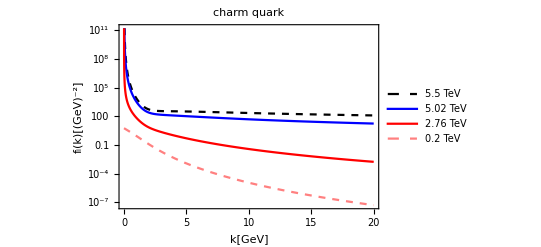

```mathematica
spec276[p_]:=Exp[(5.5-2.76)/(5.5-0.2)(Log@spec200[p]-Log@spec55[p])+Log@spec55[p]];(*2.76 TeV*)
spec502[p_]:=Exp[(5.5-5.02)/(5.5-0.2)(Log@spec200[p]-Log@spec55[p])+Log@spec55[p]];(*5.02 TeV*)
log=Show[{LogPlot[{spec55[p],spec502[p],spec276[p],spec200[p]},{p,0,20},PlotLegends->Placed[{"5.5 TeV","5.02 TeV","2.76 TeV","0.2 TeV"},{Right,Top}],PlotStyle->{{Black,Dashed},Blue,Red,{Pink,Dashed}},PlotLabel->"charm quark"]},FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
FullSimplify@spec502[p]
FullSimplify@spec276[p]
```

(1606.76 (0.1+p)^2 ((1+p^2/36)/((1+2.4596 ⅇ^(-2 p)) (1+0.27027 p)^12))^0.090566 (39.3723+p^5.5))/(p^6.5 ((1+39.3723/p^5.5)/(p+(16. p)/(0.1+p)^2))^0.090566 (16.01+p (0.2+p)))

(201.586 (0.1+p)^2 ((1+p^2/36)/((1+2.4596 ⅇ^(-2 p)) (1+0.27027 p)^12))^0.516981 (39.3723+p^5.5))/(p^6.5 ((1+39.3723/p^5.5)/(p+(16. p)/(0.1+p)^2))^0.516981 (16.01+p (0.2+p)))

```mathematica
FortranForm@FullSimplify@spec276[k]
```

```mathematica
(201.5857274467563*(0.1 + k)**2*
     -    ((1 + k**2/36.)/
     -       ((1 + 2.45960311115695/Exp(2*k))*
     -         (1 + 0.27027027027027023*k)**12)
     -       )**0.5169811320754718*
     -    (39.372261643524276 + k**5.5))/
     -  (k**6.5*((1 + 
     -         39.372261643524276/k**5.5)/
     -       (k + (16.*k)/(0.1 + k)**2))**
     -     0.5169811320754718*
     -    (16.01 + k*(0.2 + k)))
```

```mathematica
FortranForm@FullSimplify@spec502[k]
```

```mathematica
(1606.761118915908*(0.1 + k)**2*
     -    ((1 + k**2/36.)/
     -       ((1 + 2.45960311115695/Exp(2*k))*
     -         (1 + 0.27027027027027023*k)**12)
     -       )**0.09056603773584915*
     -    (39.372261643524276 + k**5.5))/
     -  (k**6.5*((1 + 
     -         39.372261643524276/k**5.5)/
     -       (k + (16.*k)/(0.1 + k)**2))**
     -     0.09056603773584915*
     -    (16.01 + k*(0.2 + k)))
```

## fik is proportional to √s_NN

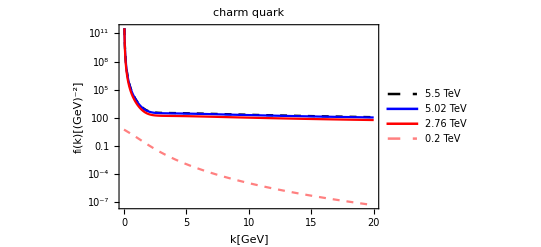

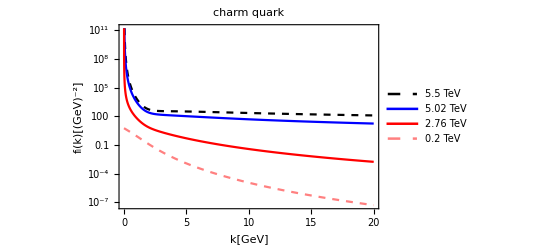

```mathematica
spec276[p_]:=(5.5-2.76)/(5.5-0.2)(spec200[p]-spec55[p])+spec55[p];(*2.76 TeV*)
spec502[p_]:=(5.5-5.02)/(5.5-0.2)(spec200[p]-spec55[p])+spec55[p];(*5.02 TeV*)

linear=Show[{LogPlot[{spec55[p],spec502[p],spec276[p],spec200[p]},{p,0,20},PlotLegends->Placed[LineLegend[{
Directive[{Black,Dashed},Thickness[0.01]],
Directive[Blue,Thickness[0.01]],
Directive[Red,Thickness[0.01]],
Directive[{Pink,Dashed},Thickness[0.01]]},{Text@Style["5.5 TeV",Bold,FontSize->20],Text@Style["5.02 TeV",Bold,FontSize->20],Text@Style["2.76 TeV",Bold,FontSize->20],Text@Style["0.2 TeV",Bold,FontSize->20]}],{Right,Top}],PlotStyle->{{Black,Dashed},Blue,Red,{Pink,Dashed}},PlotLabel->"charm quark"]},FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,20] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
spec276[p_]:=Exp[(5.5-2.76)/(5.5-0.2)(Log@spec200[p]-Log@spec55[p])+Log@spec55[p]];(*2.76 TeV*)
spec502[p_]:=Exp[(5.5-5.02)/(5.5-0.2)(Log@spec200[p]-Log@spec55[p])+Log@spec55[p]];(*5.02 TeV*)
log=Show[{LogPlot[{spec55[p],spec502[p],spec276[p],spec200[p]},{p,0,20},PlotLegends->Placed[LineLegend[{
Directive[{Black,Dashed},Thickness[0.01]],
Directive[Blue,Thickness[0.01]],
Directive[Red,Thickness[0.01]],
Directive[{Pink,Dashed},Thickness[0.01]]},{Text@Style["5.5 TeV",Bold,FontSize->20],Text@Style["5.02 TeV",Bold,FontSize->20],Text@Style["2.76 TeV",Bold,FontSize->20],Text@Style["0.2 TeV",Bold,FontSize->20]}],{Right,Top}],PlotStyle->{{Black,Dashed},Blue,Red,{Pink,Dashed}},PlotLabel->"charm quark"]},FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,20] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
Export["fikc_log.png",Show[log,ImageSize->Large],ImageResolution->500]
```

fikc_log.png

```mathematica
FortranForm[spec276[k]]
```

(2497*(1 + 
     -       39.372261643524276/k**5.5))/
     -   (k*(1 + 16/(0.1 + k)**2)) + 
     -  0.5169811320754718*
     -   ((19.2*(1 + k**2/36.))/
     -      ((1 + E**(0.9 - 2*k))*
     -        (1 + 0.27027027027027023*k)**12)
     -       - (2497*
     -        (1 + 39.372261643524276/k**5.5))
     -       /(k*(1 + 16/(0.1 + k)**2)))

```mathematica
FortranForm[spec502[k]]
```

(2497*(1 + 
     -       39.372261643524276/k**5.5))/
     -   (k*(1 + 16/(0.1 + k)**2)) + 
     -  0.09056603773584915*
     -   ((19.2*(1 + k**2/36.))/
     -      ((1 + E**(0.9 - 2*k))*
     -        (1 + 0.27027027027027023*k)**12)
     -       - (2497*
     -        (1 + 39.372261643524276/k**5.5))
     -       /(k*(1 + 16/(0.1 + k)**2)))

## fik proportional to √s_NN is even large, should be smaller at 2.76 & 5.02(Linear Combination)

```mathematica
spec276[p_]:=Exp[0.6(Log@spec200[p]-Log@spec55[p])+Log@spec55[p]];(*2.76 TeV*)
spec502[p_]:=Exp[0.2(Log@spec200[p]-Log@spec55[p])+Log@spec55[p]];(*5.02 TeV*)
```

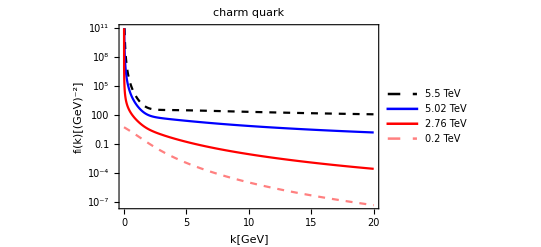

```mathematica
new=Show[{LogPlot[{spec55[p],spec502[p],spec276[p],spec200[p]},{p,0,20},PlotLegends->Placed[LineLegend[{
Directive[{Black,Dashed},Thickness[0.01]],
Directive[Blue,Thickness[0.01]],
Directive[Red,Thickness[0.01]],
Directive[{Pink,Dashed},Thickness[0.01]]},{Text@Style["5.5 TeV",Bold,FontSize->20],Text@Style["5.02 TeV",Bold,FontSize->20],Text@Style["2.76 TeV",Bold,FontSize->20],Text@Style["0.2 TeV",Bold,FontSize->20]}],{Right,Top}],PlotStyle->{{Black,Dashed},Blue,Red,{Pink,Dashed}},PlotLabel->"charm quark"]},FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,20] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
Export["improved fck.png",Show[new,ImageSize->Large],ImageResolution->500]
```

improved fck.png

```mathematica
FortranForm@FullSimplify@spec502[k]
```

(943.1810784729389*(0.1 + k)**2*
     -    ((1 + k**2/36.)/
     -       ((1 + 2.45960311115695/E**(2*k))*
     -         (1 + 0.27027027027027023*k)**12
     -         ))**0.2*
     -    (39.372261643524276 + k**5.5))/
     -  (k**6.5*((1 + 
     -         39.372261643524276/k**5.5)/
     -       (k + (16.*k)/(0.1 + k)**2))**0.2*
     -    (16.01 + k*(0.2 + k)))

```mathematica
Fi[q_,bL_]:=1/bL NIntegrate[spec276[k]*k,{k,q,q Exp[bL]}]
Fi1[q_,bL_]:=1/bL NIntegrate[spec276[k]/k*(2Pi)^3/Sqrt[1.28^2+k^2],{k,q,q Exp[bL]}]
```

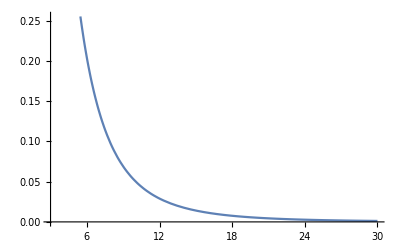

```mathematica
Plot[Fi[q,6],{q,3,30}]
```

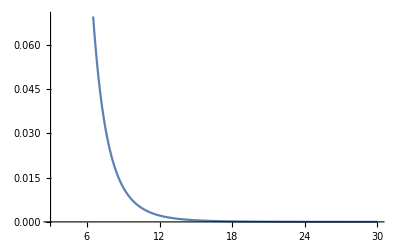

```mathematica
Plot[Fi1[q,6],{q,3,30}]
```

```mathematica
Fi[3,10]
```

0.51452

```mathematica
Fi1[3,10]
```

1.72792

## FONLL interpolation

### 5.5

```mathematica
SetDirectory[NotebookDirectory[]];
data55=Import["./charm.txt","Table"];
```

```mathematica
datafit=data55;
Do[datafit[[i,2]]=Log@data55[[i,2]],{i,1,Length[data55]}]
FindFit[datafit,Log@(a*spec55[k]*1/(Exp[(b-k)/c]+1)),{a,b,c},k]
```

FindFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

{a→3.49926×10^6,b→1.61196,c→0.578771}

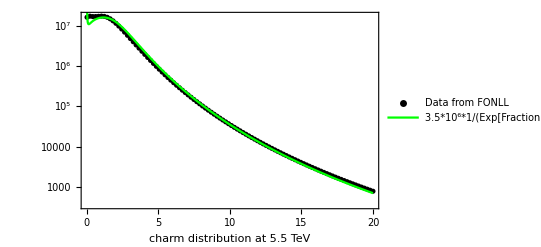

```mathematica
(*Do[data55[[i,2]]=data55[[i,2]]*1700,{i,1,Length[data55]}]*)
Show[ListLogPlot[data55,PlotStyle->Black,PlotLegends->LineLegend[{Text@Style["Data from FONLL",Bold,FontSize->15]}]],LogPlot[3.49926*^6spec55[k]*1/(Exp[(1.612-k)/0.579]+1),{k,0,20},PlotRange->All,PlotStyle->Green,PlotLegends->LineLegend[{Text@Style["3.5*10^6*1/(Exp[FractionBox[1.6 - k, 0.58]] + 1)*formula(Ref)",Bold,FontSize->15]}]],Frame->True,FrameLabel->Style["charm distribution at 5.5 TeV",Black,FontSize->20]]
```

### 200

```mathematica
SetDirectory[NotebookDirectory[]];
data200=Import["./charm_dis_200_2.txt","Table"];
```

```mathematica
Clear[datafit]
datafit=data200;
Do[datafit[[i,2]]=Log@data200[[i,2]],{i,1,Length[data200]}]
FindFit[datafit,Log@(a*spec200[k]*1/(Exp[(b-k)/c]+1)),{a,b,c},k]
```

{a→1.12834×10^7,b→0.869562,c→0.505253}

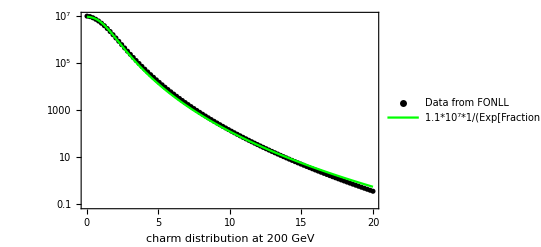

```mathematica
Show[ListLogPlot[data200,PlotStyle->Black,PlotLegends->LineLegend[{Text@Style["Data from FONLL",Bold,FontSize->15]}]],LogPlot[1/(Exp[(0.87-k)/0.5]+1)1.12834*^7*spec200[k](*1.0803486*^7spec200[k]*),{k,0,20},PlotRange->All,PlotStyle->Green,PlotLegends->LineLegend[{Text@Style["1.1*10^7*1/(Exp[FractionBox[0.87 - k, 0.5]] + 1)*formula(Ref)",Bold,FontSize->15]}]],Frame->True,FrameLabel->Style["charm distribution at 200 GeV",Black,FontSize->20]]
```

### 2.76 & 5.02

```mathematica
SetDirectory[NotebookDirectory[]];
data276=Import["./charm_dis_276_2.txt","Table"];
data502=Import["./charm_dis_502_2.txt","Table"];
```

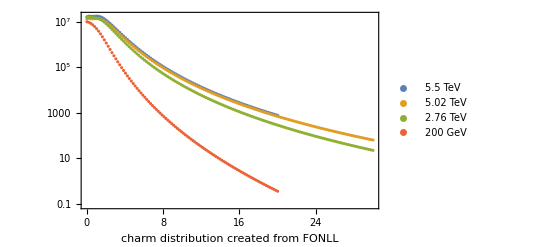

```mathematica
ListLogPlot[{data55,data502,data276,data200},PlotLegends->{"5.5 TeV","5.02 TeV","2.76 TeV","200 GeV"},Frame->True,FrameLabel->{Style["charm distribution created from FONLL",Black,FontSize->20]}]
```

```mathematica
Clear[datafit,A,b,c,d,T]
datafit=data276;
Do[datafit[[i,2]]=Log@data276[[i,2]],{i,1,Length[data276]}]
fit=FindFit[datafit,A (Exp[-b/T]ArcTan[k/b])/((1+(k/b)^d)^c),{{A,1.},{b,1.},{c,1.},{d,1.},{T,1.}},k]
(*fit=FindFit[datafit,Log[3.49926*^6 1/(Exp[(a-k)/b]+1)spec276[k]],{a,b},k]*)
```

FindFit::nrlnum: 在 {A,b,c,d,T} = {32.5136,-37.2555,-19.2017,-26.4518,32.5136} 处，函数值 {1.09550618691399×10^1812+1.78304630357534×10^1812 ⅈ,«49»,«100»} 不是由实数组成的维度为 {150} 的列表.

{A→32.5136,b→-37.2555,c→-19.2017,d→-26.4518,T→32.5136}

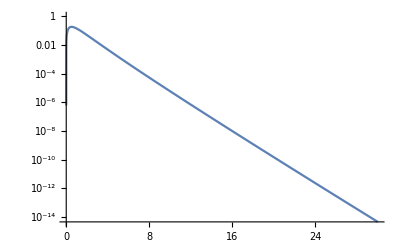

```mathematica
A=1.;b=1;c=1;d=1;T=1.;
Show[LogPlot[A (Exp[-k/T]ArcTan[k/b])/((1+(k/b)^d)^c),{k,0,30}],ListLogPlot[data276]]
```

```mathematica
f=Interpolation[data276]
```

InterpolatingFunction[…]

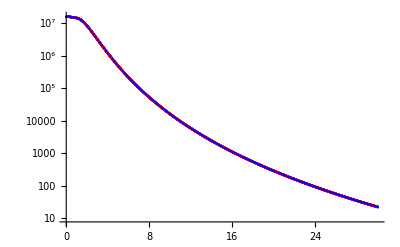

```mathematica
ListLogPlot[{Table[{k,f[k]},{k,0.01,30,0.01}],data276},PlotStyle->{{Red},{Blue}}]
```

#### 5.02

```mathematica
Clear[datafit]
datafit=data502;
Do[datafit[[i,2]]=Log@data502[[i,2]],{i,1,Length[data502]}]
fit=FindFit[datafit,Log[3.49926*^6 1/(Exp[(a-k)/b]+1)spec502[k]],{a,b},k]
```

{a→1.05249,b→0.302937}

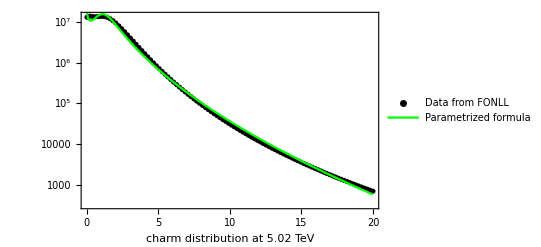

```mathematica
spec502[p_]:=ⅇ^(20.49-3.15879 p^0.5)1/(Exp[(1.05-p)/0.3029]+1);(*5.02 TeV*)
Show[ListLogPlot[data502,PlotStyle->Black,PlotLegends->LineLegend[{Text@Style["Data from FONLL",Bold,FontSize->15]}]],LogPlot[spec502[k],{k,0,20},PlotRange->All,PlotStyle->Green,PlotLegends->LineLegend[{Text@Style["Parametrized formula",Bold,FontSize->15]}]],Frame->True,FrameLabel->Style["charm distribution at 5.02 TeV",Black,FontSize->20]]
```

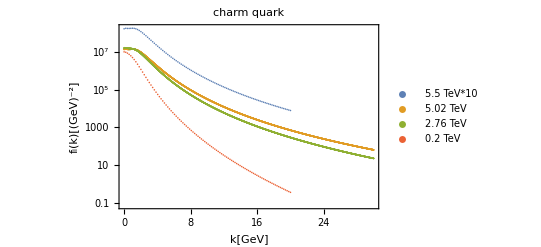

```mathematica
spec276[p_]:=Exp[20.406-3.343 p^0.5]/3.49926*^6;
spec502[p_]:=Exp[20.49-3.15879 p^0.5]/3.49926*^6;
SetDirectory[NotebookDirectory[]];
data55=Import["./charm_dis_55_2.txt","Table"];
data502=Import["./charm_dis_502.txt","Table"];
data276=Import["./charm_dis_276.txt","Table"];
data200=Import["./charm_dis_200_2.txt","Table"];
data550=data55;
Do[data550[[i,2]]=10*data55[[i,2]],{i,1,Length[data55]}]
FONLL=Show[ListLogPlot[{data550,data502,data276,data200},PlotLegends->Placed[{Text@Style["5.5 TeV*10",Bold,FontSize->20],Text@Style["5.02 TeV",Bold,FontSize->20],Text@Style["2.76 TeV",Bold,FontSize->20],Text@Style["0.2 TeV",Bold,FontSize->20]},{Right,Top}]],Frame->True,PlotLabel->"charm quark",FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,20] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},FrameStyle->Thick]
```

```mathematica
Export["charmJet.png",Show[FONLL,ImageSize->Large],ImageResolution->500]
```

charmJet.png

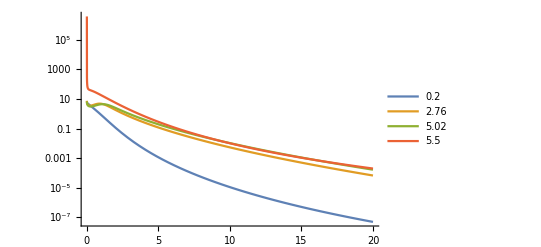

```mathematica
spec276[p_]:=Exp[20.406-3.343 p^0.5]/3.49926*^6 1/(Exp[(0.8424-p)/0.257]+1);
spec502[p_]:=Exp[20.49-3.15879 p^0.5]/3.49926*^6 1/(Exp[(1.05-p)/0.3029]+1);
LogPlot[{spec200[k],spec276[k],spec502[k],spec55[k]},{k,0,20},PlotLegends->{"0.2","2.76","5.02","5.5"},PlotRange->All]
```

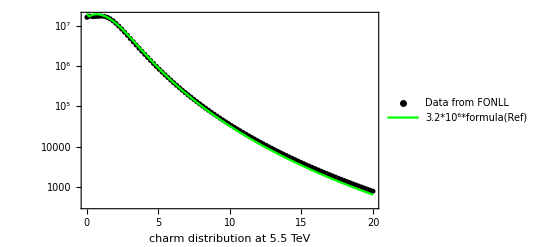

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["./charm.txt","Table"];
Show[ListLogPlot[data,PlotStyle->Black,PlotLegends->LineLegend[{Text@Style["Data from FONLL",Bold,FontSize->15]}]],LogPlot[3.205558*^6spec55[k]*1/(Exp[(1.5-k)/0.7]+1),{k,0,20},PlotRange->All,PlotStyle->Green,PlotLegends->LineLegend[{Text@Style["3.2*10^6*formula(Ref)",Bold,FontSize->15]}]],Frame->True,FrameLabel->Style["charm distribution at 5.5 TeV",Black,FontSize->20]]
```

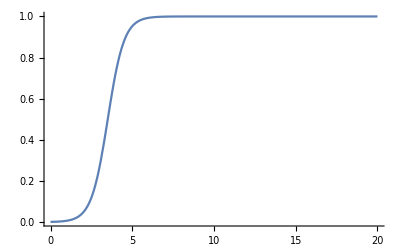

```mathematica
Plot[1/(Exp[(3.5-x)/0.5]+1),{x,0,20},PlotRange->All]
```

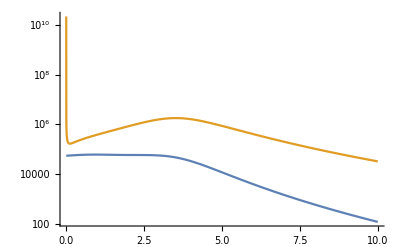

```mathematica
LogPlot[{1.0803486*^7spec200[k]*1/(Exp[(3.5-k)/0.5]+1),3.205558*^6spec55[k]*1/(Exp[(3.5-k)/0.5]+1)},{k,0,10},PlotRange->All]
```